```mathematica
$LoadFeynArts= True;
<<FeynCalc`
```

FeynCalc is already loaded! To reload it, please restart the kernel.

$Aborted

```mathematica
$D[i_]:=$dall/.TopologyList[mask__][ds__]:>TopologyList[mask][Sequence@@List[ds][[i]]];
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

> Top. 5: 1 diagram

> Top. 6: 1 diagram

> Top. 7: 1 diagram

> Top. 8: 1 diagram

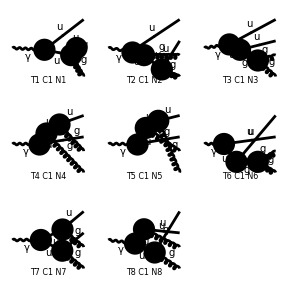

FeynArtsGraphics[{\gamma}→{u,u,g,g}][([T1 C1 N1] | [T2 C1 N2] | [T3 C1 N3]
[T4 C1 N4] | [T5 C1 N5] | [T6 C1 N6]
[T7 C1 N7] | [T8 C1 N8] | Null)]

```mathematica
Paint[$dall]
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 1 Classes insertion

> Top. 12: 1 Classes insertion

> Top. 13: 1 Classes insertion

> Top. 14: 1 Classes insertion

> Top. 15: 1 Classes insertion

> Top. 16: 1 Classes insertion

> Top. 17: 0 Classes insertions

> Top. 18: 0 Classes insertions

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 1 Classes insertion

> Top. 24: 0 Classes insertions

> Top. 25: 1 Classes insertion

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 8 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

> Top. 5: 1 diagram

> Top. 6: 1 diagram

> Top. 7: 1 diagram

> Top. 8: 1 diagram

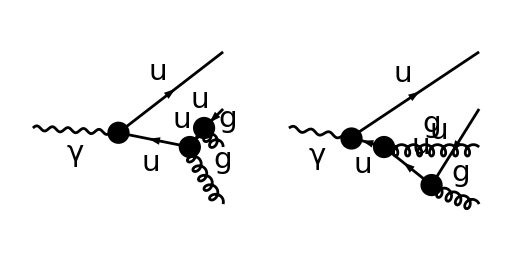

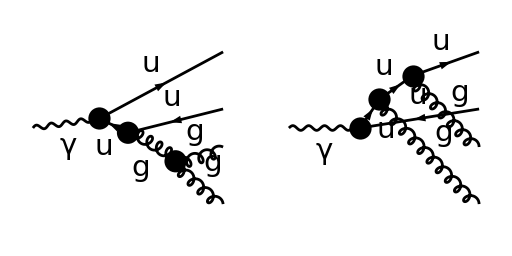

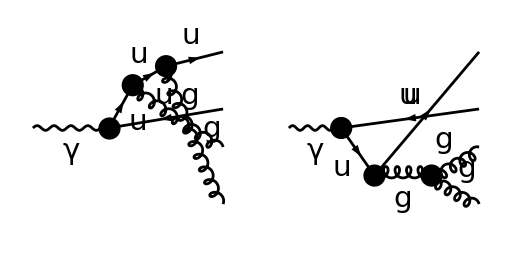

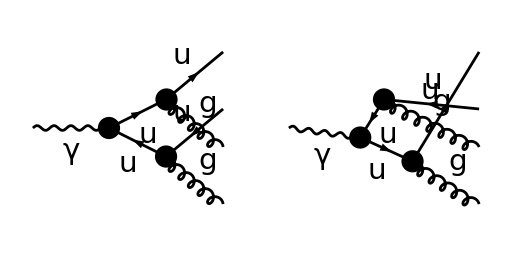

```mathematica
$top = CreateTopologies[0, 1 -> 4];
$dall = InsertFields[$top,{V[1]}->{F[3, {1}], -F[3, {1}],V[5],V[5]},
		InsertionLevel -> {Classes}, Model -> "SMQCD", ExcludeParticles -> {S[1], S[2], V[2]}];
$dtag="";
$diag=$dall+0*$D[{1,3}];
Paint[$diag, ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
$amp=FCFAConvert[CreateFeynAmp[$diag,Truncated -> False],IncomingMomenta->{q},
OutgoingMomenta->{p1,p2,p3,p4},UndoChiralSplittings->True,DropSumOver->True,List->False,SMP->True]//Contract//ChangeDimension[#,n]&
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

> Top. 5: 1 Classes amplitude

> Top. 6: 1 Classes amplitude

> Top. 7: 1 Classes amplitude

> Top. 8: 1 Classes amplitude

in total: 8 Classes amplitudes

2/3 Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[p4,-ⅈ],n],n].(DiracGamma[Momentum[p1+p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p3,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p4,n],SMP[m_u]]] SMP[e] SMP[g_s]^2 SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col6],SUNFIndex[Col3]] SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col6]]+2/3 Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[p4,-ⅈ],n],n].(DiracGamma[Momentum[p1+p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].(DiracGamma[Momentum[p1+p3+p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[q,ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p4,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p3,n]-Momentum[p4,n],SMP[m_u]]] SMP[e] SMP[g_s]^2 SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col6],SUNFIndex[Col3]] SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col6]]+2/3 Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p3-p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p4,-ⅈ],n],n].(DiracGamma[Momentum[-p2-p3,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n]+Momentum[p4,n],SMP[m_u]]] SMP[e] SMP[g_s]^2 SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col6],SUNFIndex[Col3]] SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col6]]+2/3 Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].(DiracGamma[Momentum[p1+p3,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p4,-ⅈ],n],n].(DiracGamma[Momentum[p1+p3+p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[q,ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p3,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p3,n]-Momentum[p4,n],SMP[m_u]]] SMP[e] SMP[g_s]^2 SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col2],SUNFIndex[Col6]] SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col6],SUNFIndex[Col3]]+2/3 Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].(DiracGamma[Momentum[p1+p3,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p4,-ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p3,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p4,n],SMP[m_u]]] SMP[e] SMP[g_s]^2 SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col2],SUNFIndex[Col6]] SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col6],SUNFIndex[Col3]]+2/3 Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p3-p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].(DiracGamma[Momentum[-p2-p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p4,-ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p4,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n]+Momentum[p4,n],SMP[m_u]]] SMP[e] SMP[g_s]^2 SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col2],SUNFIndex[Col6]] SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col6],SUNFIndex[Col3]]-2/3 ⅈ Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[p4,-ⅈ],n],n].(DiracGamma[Momentum[p1+p3+p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[q,ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p3,n]-Momentum[p4,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[Momentum[p3,n]+Momentum[p4,n],0]] (Pair[Momentum[p3,n],Momentum[Polarization[p3,-ⅈ],n]]+2 Pair[Momentum[p4,n],Momentum[Polarization[p3,-ⅈ],n]]) SMP[e] SMP[g_s]^2 SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},SUNFIndex[Col2],SUNFIndex[Col3]]-2/3 ⅈ Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p3-p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p4,-ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[Momentum[p3,n]+Momentum[p4,n],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n]+Momentum[p4,n],SMP[m_u]]] (Pair[Momentum[p3,n],Momentum[Polarization[p3,-ⅈ],n]]+2 Pair[Momentum[p4,n],Momentum[Polarization[p3,-ⅈ],n]]) SMP[e] SMP[g_s]^2 SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},SUNFIndex[Col2],SUNFIndex[Col3]]-2/3 ⅈ Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].(DiracGamma[Momentum[p1+p3+p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[q,ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p3,n]-Momentum[p4,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[Momentum[p3,n]+Momentum[p4,n],0]] (-2 Pair[Momentum[p3,n],Momentum[Polarization[p4,-ⅈ],n]]-Pair[Momentum[p4,n],Momentum[Polarization[p4,-ⅈ],n]]) SMP[e] SMP[g_s]^2 SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},SUNFIndex[Col2],SUNFIndex[Col3]]-2/3 ⅈ Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p3-p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[Momentum[p3,n]+Momentum[p4,n],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n]+Momentum[p4,n],SMP[m_u]]] (-2 Pair[Momentum[p3,n],Momentum[Polarization[p4,-ⅈ],n]]-Pair[Momentum[p4,n],Momentum[Polarization[p4,-ⅈ],n]]) SMP[e] SMP[g_s]^2 SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},SUNFIndex[Col2],SUNFIndex[Col3]]-2/3 ⅈ Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[p3-p4,n],n].(DiracGamma[Momentum[p1+p3+p4,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[q,ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p3,n]-Momentum[p4,n],SMP[m_u]]] FeynAmpDenominator[PropagatorDenominator[Momentum[p3,n]+Momentum[p4,n],0]] Pair[Momentum[Polarization[p3,-ⅈ],n],Momentum[Polarization[p4,-ⅈ],n]] SMP[e] SMP[g_s]^2 SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},SUNFIndex[Col2],SUNFIndex[Col3]]-2/3 ⅈ Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p3-p4,n],n]+SMP[m_u]).DiracGamma[Momentum[p3-p4,n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[Momentum[p3,n]+Momentum[p4,n],0]] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n]+Momentum[p4,n],SMP[m_u]]] Pair[Momentum[Polarization[p3,-ⅈ],n],Momentum[Polarization[p4,-ⅈ],n]] SMP[e] SMP[g_s]^2 SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTF[{SUNIndex[Glu6]},SUNFIndex[Col2],SUNFIndex[Col3]]

```mathematica
SetMandelstam[s,{-q,p1,p2,p3,p4},{1,0,0,0,0}];
```

```mathematica
$me2=$amp*(ComplexConjugate[$amp]//FCRenameDummyIndices)//
PropagatorDenominatorExplicit//FermionSpinSum//ReplaceAll[#,{DiracTrace->Tr}]&//DoPolarizationSums[#,q,0,VirtualBoson->True,GaugeTrickN->4]&//DoPolarizationSums[#,p3,0]&//DoPolarizationSums[#,p4,0]&;
```

```mathematica
$r1=$me2//SUNSimplify[#,SUNNToCACF->False]&;
```

```mathematica
$r2=$r1/.{SUNN->3,SMP["m_u"]->0,SMP["g_s"]->1,SMP["e"]->1}
```

20183+(16 6 SUNTrace[1])/(9 1^2 1 (1))+(16 ⅈ 4 SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTrace[SUNT[SUNIndex[Glu6]].SUNT[SUNIndex[Glu5]].SUNT[SUNIndex[Glu4]],Explicit→False])/(9 s[1,2]^2 s[4,5] (-s[1,2]+s[3,4]+s[4,5]))+(32 ⅈ n (1/2 s[1,5]-1/2 s[2,3]-1/2 s[3,4]) (-1/2 s[1,2]+s[3,4]+1/2 s[4,5]) (-2 s[1,2]+s[3,4]+s[4,5]) SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTrace[SUNT[SUNIndex[Glu6]].SUNT[SUNIndex[Glu5]].SUNT[SUNIndex[Glu4]],Explicit→False])/(9 s[1,2]^2 s[4,5] (-s[1,2]+s[3,4]+s[4,5]))+(32 ⅈ n (1/2-1/2 s[1,2]-1/2 s[1,5]+1/2 s[3,4]) (-1/2 s[1,2]+s[3,4]+1/2 s[4,5]) (-2 s[1,2]+s[3,4]+s[4,5]) SUNF[SUNIndex[Glu4],SUNIndex[Glu5],SUNIndex[Glu6]] SUNTrace[SUNT[SUNIndex[Glu6]].SUNT[SUNIndex[Glu5]].SUNT[SUNIndex[Glu4]],Explicit→False])/(9 s[1,2]^2 s[4,5] (-s[1,2]+s[3,4]+s[4,5]))
 |  |  |  |

```mathematica
$res = $r2/.Rule[Explicit,False]->Rule[Explicit,True]//Expand//SUNSimplify[#,SUNNToCACF->False]&
```

3584/(27 s[1,2]^2)-(1024 n)/(9 s[1,2]^2)+(128 n^2)/(9 s[1,2]^2)+(128 n^3)/(27 s[1,2]^2)-512/(3 s[1,2])+(512 n)/(3 s[1,2])-(128 n^2)/(3 s[1,2])-(16 SUNN (-1+SUNN^2))/(9 s[1,2])+5809+(8 SUNN (-1+SUNN^2) s[3,4] s[4,5])/(3 s[1,2] (1-s[1,2]-s[2,3]+s[4,5]) (-s[1,2]+s[3,4]+s[4,5]))+(8 n SUNN (-1+SUNN^2) s[3,4] s[4,5])/(9 s[1,2] (1-s[1,2]-s[2,3]+s[4,5]) (-s[1,2]+s[3,4]+s[4,5]))-(2 n^2 SUNN (-1+SUNN^2) s[3,4] s[4,5])/(9 s[1,2] (1-s[1,2]-s[2,3]+s[4,5]) (-s[1,2]+s[3,4]+s[4,5]))-(104 SUNN (-1+SUNN^2) s[3,4] s[4,5])/(9 (s[1,5]-s[2,3]-s[3,4]) (1-s[1,2]-s[2,3]+s[4,5]) (-s[1,2]+s[3,4]+s[4,5]))+(44 n SUNN (-1+SUNN^2) s[3,4] s[4,5])/(9 (s[1,5]-s[2,3]-s[3,4]) (1-s[1,2]-s[2,3]+s[4,5]) (-s[1,2]+s[3,4]+s[4,5]))-(4 n^2 SUNN (-1+SUNN^2) s[3,4] s[4,5])/(9 (s[1,5]-s[2,3]-s[3,4]) (1-s[1,2]-s[2,3]+s[4,5]) (-s[1,2]+s[3,4]+s[4,5]))
 |  |  |  |

```mathematica
Put[9/4 $res/.{n->4-2ep,SUNN->3},"~/src/eec@nlo/real/me2/test/a2qqgg_0_0"<>$dtag<>".m"]
```